# Generate the image for the poster

These files is where all the processing happens

```mathematica
Import[NotebookDirectory[]<>"ImageProcessing.wl"]
```

## Import the desired image

For best results have a clearly visible face and a plane background. If the final results aren’t ideal try editing the photo to have higher contrast and remove dust and other imperfections.

This code currently works best if the image is ~500px, so i encourage you to leave in the resizing step.

```mathematica
image =  -Graphics-;
image = ImageResize[image,500];
```

## Chose the corners and edges that will be used to define the triangulation.

*NOTE* this function internally defines two variable edges, and corners which will be used later

```mathematica
ChoosePoints[image]
```

## Use facial recognition to get important facial land marks to make sure they are included.

```mathematica
Corners = GetCorners[image];
{KeyFacePoints,NosePoint} = GetFacePoints[image];
```

## Get the pixel positions of the edges

This section extracts a list of positions of each pixel that is part of an edge. It then forces them to to be a certain distance apart. This distance calculation can take some time (1 min or less, usually closer to 15 seconds )

```mathematica
verts = ImageValuePositions[edges,White];
verts = removeAdjacentPoints[verts,20];
```

## Combine the corners and edges, facial landmarks and some random noise to interrupt uniform regions.

```mathematica
verts = verts∪Corners;
verts = verts∪KeyFacePoints;
{w,h}=ImageDimensions[image];
verts = verts∪Table[{RandomReal[{0,w}],RandomReal[{0,h}]},{idx,0,100}];
```

## Inspect the points to make sure they align with the image

```mathematica
HighlightImage[image,verts]
```

-Graphics-

## Generate the image mesh

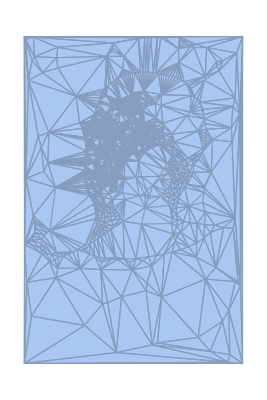

```mathematica
imageMesh=DelaunayMesh[verts]
```

## Chose a color map and color in the mesh.

See the image processing files for details on what these numbers do. Or just play around and see what you like.

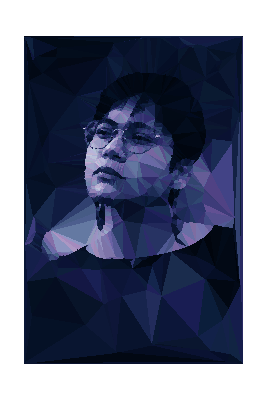

```mathematica
colorMap = CollorCorrelatedWithBrightnessAvg[.6,.2,.05,.05];

ColorImageMesh[image,imageMesh,colorMap]
```

To use the image in a poster right click on the generated image and click “Save Graphic As” and choose PDF.